```mathematica
w = 10^9;(*Основная частота*)
ϕ = 10^4;(*Уширение*)
```

```mathematica
λ = 10^8;(*Параметр функции установления прибора*)
```

```mathematica
α=0.5;(*Для управления формой импульса*)
n = 1; (*Для управления формой импульса*)
```

```mathematica
Ex[t_] := (1- 2/(ⅇ^(λ*t)+ⅇ^(-λ*t)))*(1 - 1/(1+α(Sin[ϕ*t])^2))*Sin[ϕ*t]^(2+n)*Sin[w*t];(*Переходная функция. t-время*)
```

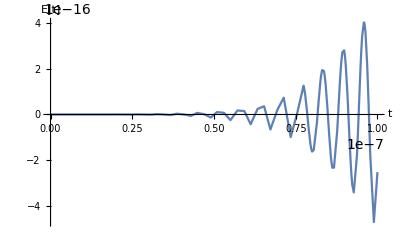

```mathematica
g1=Plot[Ex[t], {t, 0, 10^-7}, PlotRange->All,AxesLabel->{"t","E[t]"}](*График переходной функции*)
```

```mathematica
T=10^-7;(*Период*)
```

```mathematica
f1 [t_,k_]:= (1- 2/(ⅇ^(λ*(t-k*T))+ⅇ^(-λ*(t-k*T))))(*Переодическая переходная функция. t-время, k-номер периода*)
```

```mathematica
integrateResult = Integrate[(Sin[f*t])^2, {f, w-10^4, w+10^4}];(*Интегрируем синус в квадрате*)
```

```mathematica
f2[r_]:=integrateResult/.t->r(*Подставляем результат интегрирования, чтобы получить функцию от параметра t, где t - время*)
```

```mathematica
f3[t_]:=Sin[w*t](*Синус. t - время*)
```

```mathematica
f4[t_,k_]:=(1- 2/(ⅇ^(λ*(t-(k+1)*T))+ⅇ^(-λ*(t-(k+1)*T))))(*Функция, обратная переходной. t-время, k-номер периода*)
```

```mathematica
bunch[k_]:=Plot[(f1[t,k]*f2[t]*f3[t]*f4[t,k])^2, {t,T*k, (k+1)*T}, PlotRange->All](*Функция, для построения одного импульса*)
```

```mathematica
impulse[k_]:=Show[Table[bunch[i],{i,0,k,2}]];(*Импульсы с замиранием. k - кол-во импульсов*)
```

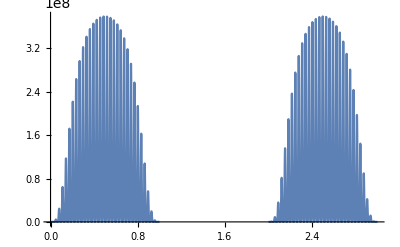

```mathematica
impulse[2]
```

```mathematica
(*tau=10^-8;
f[t_]:=Sin[10^3*t]^2*(Sin[w *t]-w*tau*Cos[w *t])
g2=Plot[f[t],{t,0,T},PlotRange->All, PlotStyle->Orange]
Show[g1,g2]*)
```

```mathematica
Q[t_]:=Sin[10^6*t]^4*(w^2*tau*Sin[w *t]^2)(*Уравнение выделения тепла. t - время*)
```

```mathematica
g3=Plot[Q[t],{t,0,30*T},PlotRange->All, PlotStyle->Green](*График выделения тепла. Время от 0 до 30*T, где Т период*)
```

-Graphics-

```mathematica
(*Plot[Integrate[(1 - 1/(1+10^6*Sin[f*t]^2))*Sin[f*t], {f, w-10^4, w+10^4}], {t, 0, 10^7}]*)
```

```mathematica
Manipulate[Plot[(1 - 1/(1+10^p(Sin[ϕ*t])^2)), {t, 0, 10^7}, PlotRange->All],{p,0,7}](*Влияние параметра p на вид функции*)
```

```mathematica
(*Integrate[(1 - 1/(1+10^2(Sin[f*t])^2))*(Sin[f*t])^2,{f, w-10^4, w+10^4 }]
int[t_]:=Integrate[(1 - 1/(1+10^2(Sin[f*t])^2))*(Sin[f*t])^2,{f, w-10^4, w+10^4 }]
Plot[int[t], {t,π/2000020000 ,π/1999980000}]*)
```